```mathematica
GUASS[time_,delay_,sigma_]:=Exp[-0.5*((time-delay)/sigma)^2]
```

```mathematica
(*Mid infrared: 0.207 eV*)
```

```mathematica
tc=0.658;
500/tc
```

759.878

```mathematica
FWHM =100  (*fs*)
sigmafs =FWHM/2.355 (*fs*)
sigma = sigmafs/tc (*1/eV*)
```

100

42.4628

64.5332

```mathematica
FWHMp =300 (*fs*)
sigmafsp =FWHMp/2.355 (*fs*)
sigmap = sigmafsp/tc (*1/eV*)
```

300

127.389

193.6

```mathematica
t0 =250/tc
```

379.939

```mathematica
omega =0.207
```

0.207

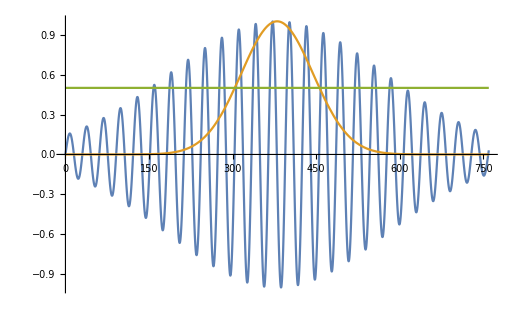

```mathematica
Plot[{GUASS[t,t0,sigmap]*Sin[omega*t],GUASS[t,t0,sigma],0.5},{t,0,500/tc}]
```

```mathematica
fac=207/3.84*1/10 (*->MC/cm*)
```

5.39063

```mathematica
{1,2,3,4,5}/fac
```

{0.185507,0.371014,0.556522,0.742029,0.927536}

```mathematica
tc=0.658;
800/tc
```

1215.81

```mathematica
FWHM =100  (*fs*)
sigmafs =FWHM/2.355 (*fs*)
sigma = sigmafs/tc (*1/eV*)
```

100

42.4628

64.5332

```mathematica
FWHMp =500 (*fs*)
sigmafsp =FWHMp/2.355 (*fs*)
sigmap = sigmafsp/tc (*1/eV*)
```

500

212.314

322.666

```mathematica
t0 =530/tc
t1 = 265/tc
```

805.471

402.736

```mathematica
omega =0.004
```

0.004

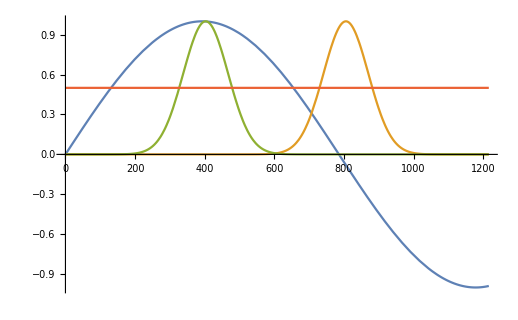

```mathematica
Plot[{Sin[omega*t],GUASS[t,t0,sigma],GUASS[t,t1,sigma],0.5},{t,0,800/tc}]
```

```mathematica
fac=4/3.84*1/10 (*->MC/cm*)
```

0.104167

```mathematica
{1}/fac
```

{9.6}